```mathematica
flow = {μ*x+y-x^2, -x+μ*y+2x^2};
fpsols = Solve[flow==0,{x,y}];
stabmat = D[flow,{{x,y}}]/.%[[2]];
stabmat//MatrixForm;
(* find unstable direction *)
eigsys = Eigensystem[stabmat];
eigenVal = Eigenvalues[stabmat]
unstabexponent = eigsys[[1,2]];
unstabdirection = eigsys[[2,2]];
```

{(-1+2 μ-√(5+9 μ^2+4 μ^3+μ^4))/(2+μ),(-1+2 μ+√(5+9 μ^2+4 μ^3+μ^4))/(2+μ)}

```mathematica
dynsys = {x'[t]== μ*x[t]+y[t]-x[t]^2,y'[t]==-x[t]+μ*y[t]+2x[t]^2};
(* start trajectory in unstable direction of saddle *)
sol[μdummy_,T_]:=Quiet@NDSolve[Join[dynsys,Thread[{x[0],y[0]}=={(1+μ^2)/(2+μ),(1-2 μ+μ^2-2 μ^3)/(2+μ)^2}-0.001*unstabdirection]]/.μ->μdummy,{x[t],y[t]},{t,0,T}];
```

SetDelayed::write: Tag List in {{x→InterpolatingFunction[{{0.,10.}},{5,7,1,{13},{4},0,0,0,0,Automatic,«3»},{{0.,0.00102648,0.00205297,1.00205,2.00205,3.00205,4.00205,5.00205,6.00205,7.00205,«3»}},{Developer`PackedArrayForm,{0,2,4,6,8,10,12,14,16,18,«4»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«16»}},{Automatic}],y→InterpolatingFunction[{{0.,10.}},«3»,{Automatic}]}}[μdummy_,T_] is Protected.

ReplaceAll::reps: {{{x→InterpolatingFunction[{{0.,10.}},{5,7,1,{13},{4},0,0,0,0,Automatic,«3»},{{0.,0.00102648,0.00205297,1.00205,2.00205,3.00205,4.00205,5.00205,6.00205,7.00205,«3»}},{Developer`PackedArrayForm,{0,2,4,6,8,10,12,14,16,18,«4»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«16»}},{Automatic}],y→InterpolatingFunction[{{0.,10.}},{5,7,1,{13},{4},0,0,0,0,Automatic,«3»},«1»,{Developer`PackedArrayForm,{«1»},{0.,«9»,«16»}},{Automatic}]}}[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

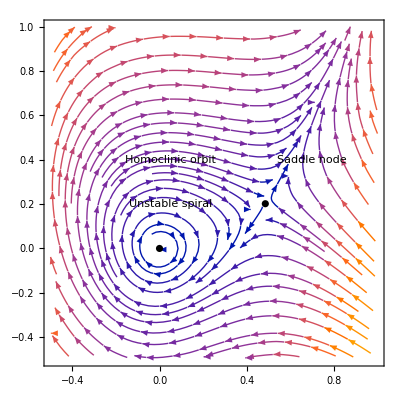

```mathematica
(* critical value μc=-0.8645, see Lecture notes *)
μval = 0.066;
Tmax = 1000;
text = Graphics[Text["μ = 0.066", {-0.4,-0.55}]];
text2 = Graphics[Text["Saddle node", {0.7, 0.4}]];
text3 = Graphics[Text["Unstable spiral", {0.05,0.2}]];
text4 = Graphics[Text["Homoclinic orbit", {0.05, 0.4}]];
p0 =Show[StreamPlot[flow/.μ->μval,{x,-0.5,1},{y,-0.5,1}],ParametricPlot[Evaluate[{x[t],y[t]}/.sol[μval,Tmax]],{t,800,Tmax},PlotStyle->Red,PlotRange->{{-0.5,0.5},{-0.5,0.5}}], ListPlot[{x,y}/.fpsols/.μ->μval,PlotRange->{{-1.5,1.5},{-1.5,1.5}},PlotStyle->Black], text, text2, text3, text4];
(p0//Normal)/.Line[x_]:>{Arrowheads[{0.05,0.05,0.05}],Arrow[x]}
```

NDSolve::ndnco: The number of constraints (0) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (2).

SetDelayed::write: Tag List in {{x→InterpolatingFunction[{{0.,10.}},{5,7,1,{13},{4},0,0,0,0,Automatic,«3»},{{0.,0.00102648,0.00205297,1.00205,2.00205,3.00205,4.00205,5.00205,6.00205,7.00205,«3»}},{Developer`PackedArrayForm,{0,2,4,6,8,10,12,14,16,18,«4»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«16»}},{Automatic}],y→InterpolatingFunction[{{0.,10.}},«3»,{Automatic}]}}[x0_,y0_] is Protected.

ReplaceAll::reps: {{{x→InterpolatingFunction[{{0.,10.}},{5,7,1,{13},{4},0,0,0,0,Automatic,«3»},{{0.,0.00102648,0.00205297,1.00205,2.00205,3.00205,4.00205,5.00205,6.00205,7.00205,«3»}},{Developer`PackedArrayForm,{0,2,4,6,8,10,12,14,16,18,«4»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«16»}},{Automatic}],y→InterpolatingFunction[{{0.,10.}},{5,7,1,{13},{4},0,0,0,0,Automatic,«3»},«1»,{Developer`PackedArrayForm,{«1»},{0.,«9»,«16»}},{Automatic}]}}[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

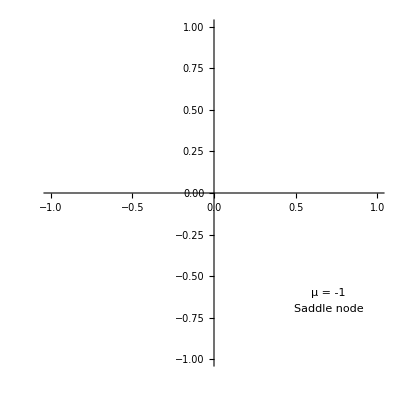

-Graphics-

```mathematica
μ = 0.07;
s=NDSolve[{x'[t]== μ*x[t]+y[t]-x[t]^2,y'[t]==-x[t]+μ*y[t]+2x[t]^2},{x[t],y[t]},{t,0,10}];
minx=-1;
miny=-1;
maxx=1;
maxy=1;
dist=0.1;
sol[x0_,y0_]:=NDSolve[{x'[t]== μ*x[t]+y[t]-x[t]^2,y'[t]==-x[t]+μ*y[t]+2x[t]^2,x[0]==x0,y[0]==y0},{x,y},{t,10}];
inits=Join[Table[{minx,y},{y,miny,maxy,dist}],Table[{maxx,y},{y,miny,maxy,dist}],Table[{x,miny},{x,minx,maxx,dist}],Table[{x,maxy},{x,minx,maxx,dist}]];
text = Graphics[Text["μ = -1", {0.7,-0.6}]];
text2 = Graphics[Text["Saddle node", {0.7, -0.7
}]];
p0 =Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol[inits[[i,1]],inits[[i,2]]]],{t,0,10},PlotRange->{{minx,maxx},{miny,maxy}}],{i,Length[inits]}], text, text2, ParametricPlot[Evaluate[{x[t],y[t]}/.sol[μ,Tmax]],{t,0,Tmax},PlotStyle->Red,PlotRange->{{-0.5,0.5},{-0.5,0.5}}]]
(p0//Normal)/.Line[x_]:>{Arrowheads[{0,0.05,0}],Arrow[x]}
```